# Dados dos diferentes circuitos de transmissão de energia elétrica

## Antonio Carlos Siqueira de Lima outubro 2020

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/Transmissão-2020/arquivos_MMA_EE457

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,
Axes-> False,Frame-> True,PlotRange->All];
```

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Dados dos condutores de fase

### Bluejay

```mathematica
r0=8.702 10^3;   (* [m]*)
r1=15.977 *10^-3;
ρϕ=29.544 10^-9;(* Ω/m] *)
```

### Rail

```mathematica
r0=8.702 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.796 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
```

### Ruddy

```mathematica
r0=7.821 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.364 10^-3;
ρϕ=29.559 10^-9;  (* [Ω/m] *)
```

### Grossbeak

```mathematica
r0=7.456 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 12.573 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
```

### Dove

```mathematica
r0=6.988 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 11.773 10^-3;
ρϕ=29.567 10^-9;  (* [Ω/m] *)
```

### Penguim

```mathematica
r0=4.123 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 7.150 10^-3;
ρϕ=28.554 10^-9;  (* [Ω/m] *)
```

### Leghorn

```mathematica
r0=4.840 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.7180 10^-3;
ρϕ=29.586 10^-9;  (* [Ω/m] *)
```

### Minorca

```mathematica
r0=4.390 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.0960 10^-3;
ρϕ=29.579 10^-9;  (* [Ω/m] *)
```

### 3/8 EHS

```mathematica
r0=0.0;(* ⟹ [m] ⟸ *)
r1 = 4.570 10^-3;
ρϕ=276.470 10^-9;  (* [Ω/m] *)
```

## Visualizando algumas linhas de campo

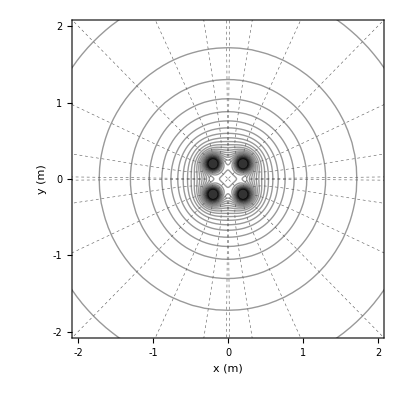

## Disposição dos condutores

### 750 kV - Bluejay

```mathematica
db=.475;
xc0= {-15.85,0, 15.85};
xc=Flatten@Outer[Plus,xc0,db Cos[π/4 +#1 π/2]&@Range[0,3]];xc=Flatten[Join[xc,{-14.45,14.45}]];
fc = 20.9;
yc0= {35.9 , 35.9, 35.9}-2/3 fc;
yc1={45.9,45.9}- 2/3 14.7;
yc= Flatten@Outer[Plus,yc0,db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc= Flatten[Join[yc,yc1]];
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

### 500 kV Convencional - Rail

```mathematica
xy3={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},{0.000,10.736},{0.229,11.132},{-0.229,11.132},{11.000,10.736},{10.771,11.132},{11.229,11.132},{-6.000,22.000},{6.000,22.000}};;
```

```mathematica
mostra3={Circle[#,.25]}&/@xy3;
```

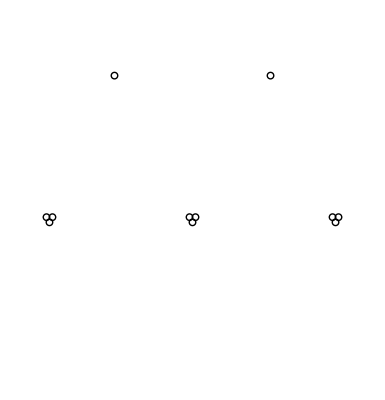

```mathematica
t3=Show[Graphics[mostra3],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

### 500 kV Compacto - Rail

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra4={Circle[#,.25]}&/@xy4;
```

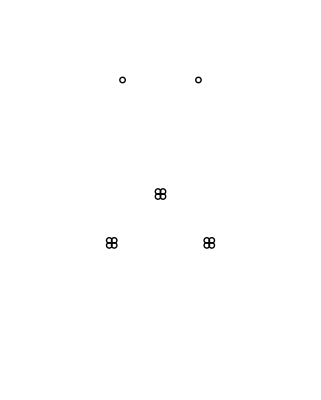

```mathematica
t4=Show[Graphics[mostra4],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,30}},FrameLabel->{"distância (m)","distância (m)"}]
```

### 500 kV - Rail

```mathematica
db=.475;
xc=Flatten@Outer[Plus,{6,11,6+9},db Cos[π/4 +#1 π/2]&@Range[0,3]];
xc=Flatten[Join[xc,-xc]];
yc=Flatten@Outer[Plus,{27.7-4.5,27.7+10-4.5, 27.7-4.5},db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc=Flatten[Join[yc,yc]];
xc=Flatten[Join[xc,{8.8,-8.8}]];
yc=Flatten[Join[yc,{27.7+10+5,27.7+10+5}]];
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## 500 kV Recapacitado - Rail

```mathematica
xy2={{-7.229, 8.639}, {-7.229, 10.500}, {-6.771, 10.500}, {-6.771, 8.639}, {-0.229, 10.500},
{-0.229, 9.876}, {0.229, 9.876}, {0.229, 10.500}, {7.229, 8.639}, {7.229, 10.500}, {6.771, 10.500},
{6.771, 8.639}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
```

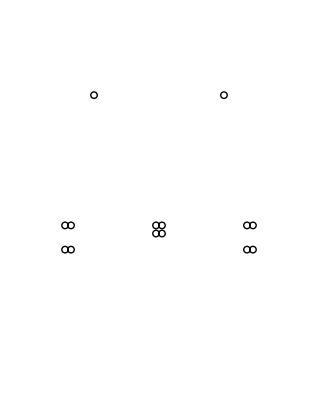

```mathematica
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-.10,25}},FrameLabel->{"x (m)","y (m)"}]
```

## 345kV - Ruddy

```mathematica
xy1={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy1;
```

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10.1,10.1},{0,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

## Obter Z1, Y1 e a potência característica